## Attemp

```mathematica
Grid[Table[,{4},{4}],Frame->{None,None, {{1,1}-> True,{1,2}-> True,{2,3}-> True,{3,4}-> True}}]
```

|  |  | 
 |  |  | 
 |  |  | 
 |  |  |

## yi-bonds

### Indegriant

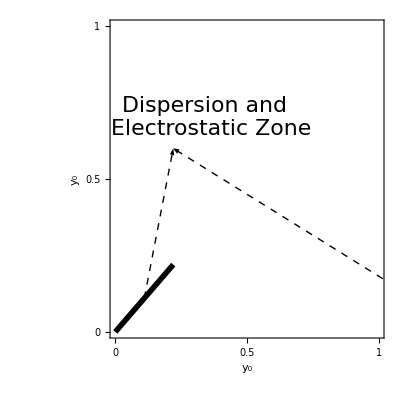

```mathematica
(*y0y0=Graphics[{ {Thickness[0.01],Line[{{0.0,0.0},{0.22,0.22}}]}, {Dashed,Arrow[{{0.11,0.11},{0.22,0.6}}]},
{Dashed,Arrow[{{1.06,0.15},{0.22,0.6}}]}, {Text[Style["Dispersion and \n Electrostatic Zone",Medium,Bold,Italic,22],{0.35,0.7},{0,0},{1,0}]} },PlotRange-> {{0,1},{0,1}},Frame-> True,FrameStyle-> Thick,FrameTicks-> {{{{0,0},{0.5,0.5},{1.0,1}},{}},{{{0,0},{0.5,0.5},{1.0,1}},{}}},FrameTicksStyle->Directive[Bold,18],FrameLabel-> {Style[Subscript[y, 0],Bold,24],Style[Subscript[y, 0],Bold,24]},LabelStyle-> {Thick}]*)
y0y0=Graphics[{ {Thickness[0.01],Line[{{0.0,0.0},{0.22,0.22}}]}, {Dashed,Arrow[{{0.11,0.11},{0.22,0.6}}]},
{Dashed,Arrow[{{1.06,0.15},{0.22,0.6}}]}, {Text[Style["Dispersion and \n Electrostatic Zone",Medium,Italic,22],{0.35,0.7},{0,0},{1,0}]} },PlotRange-> {{0,1},{0,1}},Frame-> True,FrameTicks-> {{{{0,0},{0.5,0.5},{1.0,1}},{}},{{{0,0},{0.5,0.5},{1.0,1}},{}}},FrameTicksStyle->Directive[18],FrameLabel-> {Style[Subscript[y, 0],24],Style[Subscript[y, 0],24]},LabelStyle-> {Thick}]
```

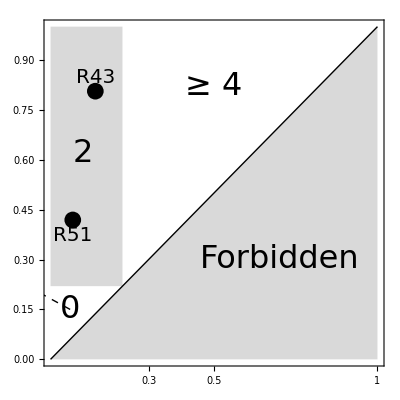

```mathematica
(*y0y1=Graphics[{  {LightGray,Polygon[{{1,0},{2,0},{2,1}}]},{LightGray,Polygon[{{1,0.22},{1.22,0.22},{1.22,1},{1,1}}]}, {Thickness[0.005],Line[{{1,0},{2,1}}]},
{Dashed,Arrow[{{1.06,0.15},{0.22,0.6}}]}, {Text[Style["≥ 4",Medium,Bold,Italic,32],{1.5,0.82},{0,0}]},{Text[Style["2",Medium,Bold,Italic,32],{1.1,0.62},{0,0}]},{PointSize[0.03],Point[{1.068,0.419}]} ,{Text[Style["R51",Italic,20],{1.068,0.4},{0,1}]},{PointSize[0.03],Point[{1.137,0.806}]},{Text[Style["R43",Italic,20],{1.137,0.82},{0,-1}]},
{Text[Style["0",Medium,Bold,Italic,32],{1.06,0.15},{0,0}]}, {Text[Style["Forbidden",Medium,Bold,Italic,32],{1.7,0.3},{0,0}]} },PlotRange-> {{1,2},{0,1}},Frame-> True,FrameStyle-> Thick,FrameTicks-> {{{},{}},{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}}},FrameTicksStyle->Directive[Bold,12],FrameLabel-> {Style[Subscript[y, 1],Bold,24](*,Style[Subscript[y, 0],Bold,17]*)},LabelStyle-> {Thick}]*)
y0y1=Graphics[{  {LightGray,Polygon[{{1,0},{2,0},{2,1}}]},{LightGray,Polygon[{{1,0.22},{1.22,0.22},{1.22,1},{1,1}}]}, {Line[{{1,0},{2,1}}]},
{Dashed,Arrow[{{1.06,0.15},{0.22,0.6}}]}, {Text[Style["≥ 4",Medium,Italic,32],{1.5,0.82},{0,0}]},{Text[Style["2",Medium,Italic,32],{1.1,0.62},{0,0}]},{PointSize[0.03],Point[{1.068,0.419}]} ,{Text[Style["R51",Italic,20],{1.068,0.4},{0,1}]},{PointSize[0.03],Point[{1.137,0.806}]},{Text[Style["R43",Italic,20],{1.137,0.82},{0,-1}]},
{Text[Style["0",Medium,Italic,32],{1.06,0.15},{0,0}]}, {Text[Style["Forbidden",Medium,Italic,32],{1.7,0.3},{0,0}]} },PlotRange-> {{1,2},{0,1}},Frame-> True,FrameTicks-> {{{},{}},{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}}},FrameTicksStyle->Directive[18],FrameLabel-> {Style[Subscript[y, 1],24](*,Style[Subscript[y, 0],Bold,17]*)}]
```

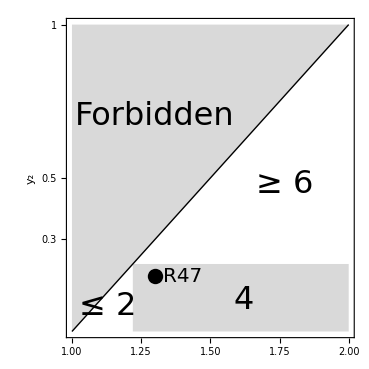

```mathematica
(*y1y2=Graphics[{  {LightGray,Polygon[{{1,1},{1,2},{2,2}}]},{LightGray,Polygon[{{1.22,1},{1.22,1.22},{2,1.22},{2,1}}]}, {Thickness[0.005],Line[{{1,1},{2,2}}]},
{Text[Style["≥ 6",Medium,Bold,Italic,32],{1.77,1.48},{0,0}]},
{Text[Style["4",Medium,Bold,Italic,32],{1.62,1.1},{0,0}]}, 
{Text[Style["≤ 2",Medium,Bold,Italic,32],{1.13,1.08},{0,0},{1.0,0.5}]},{Text[Style["Forbidden",Medium,Bold,Italic,32],{1.3,1.7},{0,0}]},{PointSize[0.03],Point[{1.30,1.18}]} ,{Text[Style["R47",Italic,20],{1.33,1.18},{-1,0}]} },PlotRange-> {{1,2},{1,2}},Frame-> True,FrameStyle-> Thick,FrameTicks-> {{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}},{{},{}}},FrameTicksStyle->Directive[Bold,12],FrameLabel-> {(*Style[Subscript[y, 1],Bold,17]*),Style[Subscript[y, 2],Bold,24]},LabelStyle-> {Thick}]*)
y1y2=Graphics[{  {LightGray,Polygon[{{1,1},{1,2},{2,2}}]},{LightGray,Polygon[{{1.22,1},{1.22,1.22},{2,1.22},{2,1}}]}, {Line[{{1,1},{2,2}}]},
{Text[Style["≥ 6",Medium,Italic,32],{1.77,1.48},{0,0}]},
{Text[Style["4",Medium,Italic,32],{1.62,1.1},{0,0}]}, 
{Text[Style["≤ 2",Medium,Italic,32],{1.13,1.08},{0,0},{1.0,0.5}]},{Text[Style["Forbidden",Medium,Italic,32],{1.3,1.7},{0,0}]},{PointSize[0.03],Point[{1.30,1.18}]} ,{Text[Style["R47",Italic,20],{1.33,1.18},{-1,0}]} },PlotRange-> {{1,2},{1,2}},Frame-> True,FrameTicks-> {{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}},{{},{}}},FrameTicksStyle->Directive[18],FrameLabel-> {(*Style[Subscript[y, 1],Bold,17]*),Style[Subscript[y, 2],24]}]
```

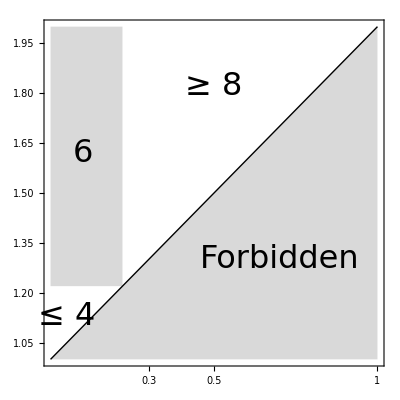

```mathematica
(*y2y3=Graphics[{  {LightGray,Polygon[{{1,1},{2,1},{2,2}}]},{LightGray,Polygon[{{1,1.22},{1.22,1.22},{1.22,2},{1,2}}]}, {Thickness[0.005],Line[{{1,1},{2,2}}]},
{Text[Style["≥ 8",Medium,Bold,Italic,32],{1.5,1.82}]},
{Text[Style["6",Medium,Bold,Italic,32],{1.1,1.62},{0,0}]}, {Text[Style["≤ 4",Medium,Bold,Italic,32],{1.05,1.13},{0,0},{0.5,0.5}]},{Text[Style["Forbidden",Medium,Bold,Italic,32],{1.7,1.3},{0,0}]} },PlotRange-> {{1,2},{1,2}},Frame-> True,FrameStyle-> Thick,FrameTicks-> {{{},{}},{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}}},FrameTicksStyle->Directive[Bold,12],FrameLabel-> {Style[Subscript[y, 3],Bold,24](*,Style[Subscript[y, 2],Bold,17]*)},LabelStyle-> {Thick}]*)
y2y3=Graphics[{  {LightGray,Polygon[{{1,1},{2,1},{2,2}}]},{LightGray,Polygon[{{1,1.22},{1.22,1.22},{1.22,2},{1,2}}]}, {Line[{{1,1},{2,2}}]},
{Text[Style["≥ 8",Medium,Italic,32],{1.5,1.82}]},
{Text[Style["6",Medium,Italic,32],{1.1,1.62},{0,0}]}, {Text[Style["≤ 4",Medium,Italic,32],{1.05,1.13},{0,0},{0.5,0.5}]},{Text[Style["Forbidden",Medium,Italic,32],{1.7,1.3},{0,0}]} },PlotRange-> {{1,2},{1,2}},Frame-> True,FrameTicks-> {{{},{}},{{{1.3,0.3},{1.5,0.5},{2.0,1}},{}}},FrameTicksStyle->Directive[18],FrameLabel-> {Style[Subscript[y, 3],24](*,Style[Subscript[y, 2],Bold,17]*)}]
```

### Combination1

```mathematica
Graphics[{Text[Style["a''",Medium,Bold,Italic,30],{1.5,1.82}]}]
```

-Graphics-

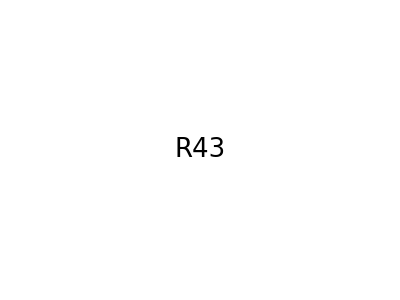

```mathematica
Graphics[{Text[Style["R43",Medium,Italic,26],{1.5,1.82}]}]
```

```mathematica
Graphics[{Text[Style["",Medium,Italic,26],{1.5,1.82}]}]
```

```mathematica
Graphics[{{ White,Rectangle[{0,0},{3,3}]},Inset[y0y0],Inset[y0y1],Inset[y1y2],Inset[y2y3]}]
```

```mathematica
Directory[]
```

C:\Users\dodo\Documents

```mathematica
Export["Figure1.tiff",Out[5],"TIFF",ImageResolution->600]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

### Combination2

```mathematica
Graphics[{{ White,Rectangle[{0,0},{3,3}]},Inset[y0y0],Inset[y0y1],Inset[y1y2],Inset[y2y3]}]
```

### Combination3

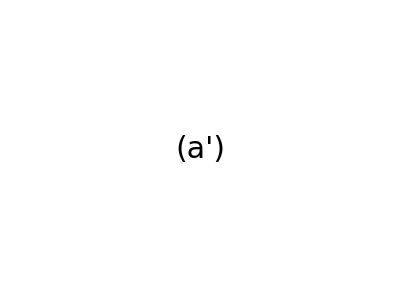

```mathematica
Graphics[{Text[Style["(a')",Medium,Italic,30],{1.5,1.82}]}]
```

```mathematica
Graphics[{Text[Style["R43",Medium,Italic,26],{1.5,1.82}]}]
```

-Graphics-

```mathematica
Graphics[{{ White,Rectangle[{0,0},{3,3}]},Inset[y0y0],Inset[y0y1],Inset[y1y2],Inset[y2y3]}]
```

## HOMA R51,R47,R75

### functions

```mathematica
homagraph[cen_,side_,homa_]:={{EdgeForm[{Black}],GrayLevel[(1-homa)],Polygon[{{cen⟦1⟧,cen⟦2⟧+side/(√3)},{cen⟦1⟧+side/2,cen⟦2⟧+side/(2 √3)},{cen⟦1⟧+side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧,cen⟦2⟧-side/(√3)},{cen⟦1⟧-side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧-side/2,cen⟦2⟧+side/(2 √3)}}]} ,{Text[Style[N[Round[homa*100]/100,2],Medium(*,Bold*),Italic,22],cen,{0,0}]}}
```

```mathematica
pahhoma[cen_,side_,homa_,zigzag_,armchair_]:=Graphics[ Table[homagraph[{cen⟦1⟧+j*side+Mod[i,2]*side/2,cen⟦2⟧-i*(√3)/2*side},side,homa⟦(j+1+i*zigzag)⟧],{i,0,armchair-1},{j,0,zigzag-1}] ]
```

```mathematica
pahhomaMultiRow[cen_,side_,homa_,zigzag_,armchair_]:=Graphics[{Table[homagraph[{cen⟦1⟧+k*side,cen⟦2⟧},side,homa⟦k+1⟧],{k,0,zigzag-1}], Table[homagraph[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side/2+Mod[j+1,zigzag]*side,cen⟦2⟧-(2*i+1)*(√3)/2*side-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side},side,homa⟦(zigzag+j+1+i*(2*zigzag-1))⟧],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }]
```

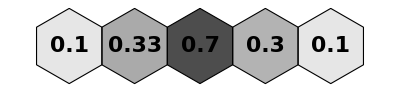

```mathematica
pahhoma[{0,0},1,{0.1,0.333,0.7,0.3,0.1},5,1]
```

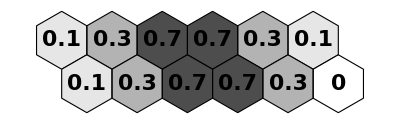

```mathematica
pahhoma[{0,0},√3,{0.1,0.3,0.7,0.7,0.3,0.1,0.1,0.3,0.7,0.7,0.3,0},6,2]
```

### yi

```mathematica
yi[x_,y_]:=1-(x-y)/(1+(x-y)^2/4)
```

```mathematica
yi[1.00219,0.99781]
```

0.99562

```mathematica
yi[1.77351,0.22649]
```

0.0320948

### R31

```mathematica
homa31={0.463557460871,0.786543908849,0.463557460871}
```

{0.463557,0.786544,0.463557}

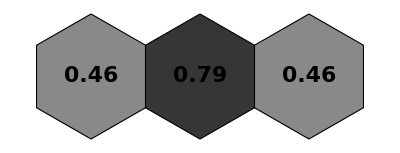

```mathematica
pahhoma[{0,0},1,homa31,3,1]
```

### R41

```mathematica
homa41={0.282931413033,0.677232315056,0.677232315055,0.282931413032}
```

{0.282931,0.677232,0.677232,0.282931}

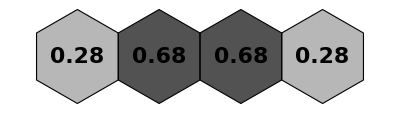

```mathematica
pahhoma[{0,0},1,homa41,4,1]
```

### R51

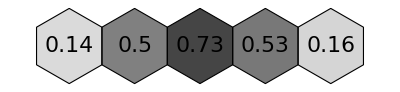

```mathematica
pahhoma[{0,0},1,{0.143871835232,0.499531181133,0.728790576973,0.529179021736,0.164809564176},5,1]
```

### R71

```mathematica
homa71={0.0105501681571,0.244443802832,0.544551148414,0.699724253075,0.544551147851,0.24444379915,0.0105501626926}
```

{0.0105502,0.244444,0.544551,0.699724,0.544551,0.244444,0.0105502}

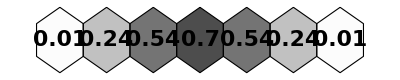

```mathematica
pahhoma[{0,0},1,homa71,7,1]
```

### R47 [y0=0.95, y1=0.26, y2=0.18], [y0=0.99,y1=0.30]

```mathematica
homa47={0.454311122852,0.685352899729,0.685358468623,0.454343312876,0.17316715308,0.377818229507,0.17318086729,0,0.601818245152,0.633778363098,0.633778177179,0.601804293371,0.240626877496,0.422299592281,0.240609519422,0,0.601830545988,0.633786322291,0.633775331015,0.601806451353,0.173188681002,0.377818516836,0.173187150124,0,0.454308646364,0.685344492842,0.685361531294,0.454346494089}
```

{0.454311,0.685353,0.685358,0.454343,0.173167,0.377818,0.173181,0,0.601818,0.633778,0.633778,0.601804,0.240627,0.4223,0.24061,0,0.601831,0.633786,0.633775,0.601806,0.173189,0.377819,0.173187,0,0.454309,0.685344,0.685362,0.454346}

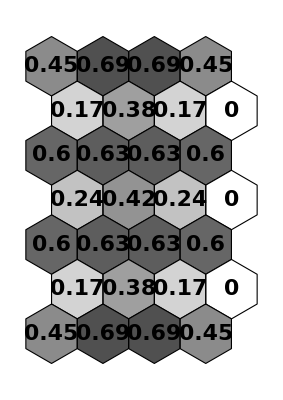

```mathematica
pahhoma[{0,0},1,homa47,4,7]
```

```mathematica
homa47n={0.454311122852,0.685352899729,0.685358468623,0.454343312876,0.17316715308,0.377818229507,0.17318086729,0.601818245152,0.633778363098,0.633778177179,0.601804293371,0.240626877496,0.422299592281,0.240609519422,0.601830545988,0.633786322291,0.633775331015,0.601806451353,0.173188681002,0.377818516836,0.173187150124,0.454308646364,0.685344492842,0.685361531294,0.454346494089}
```

{0.454311,0.685353,0.685358,0.454343,0.173167,0.377818,0.173181,0.601818,0.633778,0.633778,0.601804,0.240627,0.4223,0.24061,0.601831,0.633786,0.633775,0.601806,0.173189,0.377819,0.173187,0.454309,0.685344,0.685362,0.454346}

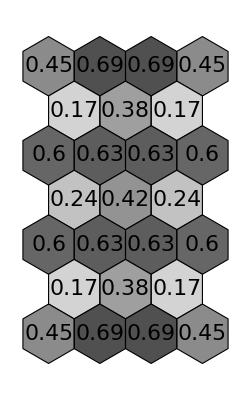

```mathematica
pahhomaMultiRow[{0,0},1,homa47n,4,7]
```

### R75 [y0=0.99,y1=0.03]

```mathematica
homa75={0.686594630562,0.66608312452,0.513237532036,0.509467265817,0.513231054067,0.666072113511,0.686601466608,0.23874361626,0.556582901003,0.673299910988,0.673300531945,0.556582118652,0.238752521381,0,0.785604747234,0.580018816884,0.492950459309,0.51493847142,0.492948046011,0.580013836936,0.785607265665,0.215797701799,0.529683864936,0.654976808313,0.654972766894,0.529693111215,0.21579469412,0,0.711167816814,0.660647425242,0.383694631368,0.280950289949,0.383680353071,0.660630973298,0.711161969016}
```

{0.686595,0.666083,0.513238,0.509467,0.513231,0.666072,0.686601,0.238744,0.556583,0.6733,0.673301,0.556582,0.238753,0,0.785605,0.580019,0.49295,0.514938,0.492948,0.580014,0.785607,0.215798,0.529684,0.654977,0.654973,0.529693,0.215795,0,0.711168,0.660647,0.383695,0.28095,0.38368,0.660631,0.711162}

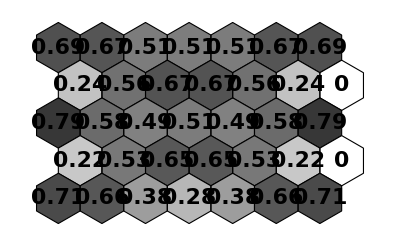

```mathematica
pahhoma[{0,0},1,homa75,7,5]
```

```mathematica
homa75n={0.686594630562,0.66608312452,0.513237532036,0.509467265817,0.513231054067,0.666072113511,0.686601466608,0.23874361626,0.556582901003,0.673299910988,0.673300531945,0.556582118652,0.238752521381,0.785604747234,0.580018816884,0.492950459309,0.51493847142,0.492948046011,0.580013836936,0.785607265665,0.215797701799,0.529683864936,0.654976808313,0.654972766894,0.529693111215,0.21579469412,0.711167816814,0.660647425242,0.383694631368,0.280950289949,0.383680353071,0.660630973298,0.711161969016}
```

{0.686595,0.666083,0.513238,0.509467,0.513231,0.666072,0.686601,0.238744,0.556583,0.6733,0.673301,0.556582,0.238753,0.785605,0.580019,0.49295,0.514938,0.492948,0.580014,0.785607,0.215798,0.529684,0.654977,0.654973,0.529693,0.215795,0.711168,0.660647,0.383695,0.28095,0.38368,0.660631,0.711162}

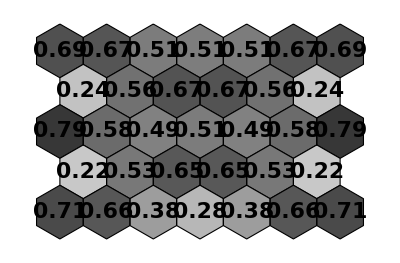

```mathematica
pahhomaMultiRow[{0,0},1,homa75n,7,5]
```

### R43

```mathematica
homa43={0.382287349247,0.684576774848,0.684572302344,0.38228539165,0.0485844425483,0.276155061772,0.0485844424247,0.382287349258,0.684576774847,0.684572302337,0.382285391655}
```

{0.382287,0.684577,0.684572,0.382285,0.0485844,0.276155,0.0485844,0.382287,0.684577,0.684572,0.382285}

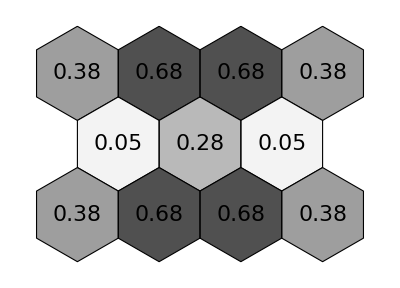

```mathematica
pahhomaMultiRow[{0,0},1,homa43,4,3]
```

### R53

```mathematica
homa53={0.307450592695,0.587001865207,0.701488637018,0.587001865219,0.307450592744,0.0382969279191,0.326428190147,0.326428190148,0.0382969280209,0.307450592727,0.58700186524,0.701488637037,0.58700186525,0.307450592739}
```

{0.307451,0.587002,0.701489,0.587002,0.307451,0.0382969,0.326428,0.326428,0.0382969,0.307451,0.587002,0.701489,0.587002,0.307451}

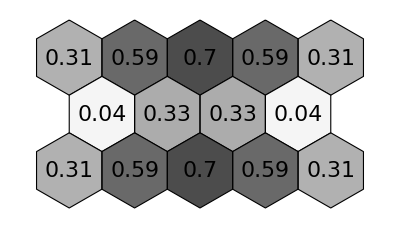

```mathematica
pahhomaMultiRow[{0,0},1,homa53,5,3]
```

## Surface Growth Site

### function

```mathematica
benzenegraph[cen_,side_]:={{EdgeForm[{Black}],GrayLevel[(1-0)],Polygon[{{cen⟦1⟧,cen⟦2⟧+side/(√3)},{cen⟦1⟧+side/2,cen⟦2⟧+side/(2 √3)},{cen⟦1⟧+side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧,cen⟦2⟧-side/(√3)},{cen⟦1⟧-side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧-side/2,cen⟦2⟧+side/(2 √3)}}]} };
pahgraph[cen_,side_,zigzag_,armchair_]:=Graphics[ Table[benzenegraph[{cen⟦1⟧+j*side+Mod[i,2]*side/2,cen⟦2⟧-i*(√3)/2*side},side],{i,0,armchair-1},{j,0,zigzag-1}] ];
pahgraphMultiRow[cen_,side_,zigzag_,armchair_]:=Graphics[{Table[benzenegraph[{cen⟦1⟧+k*side,cen⟦2⟧},side],{k,0,zigzag-1}], Table[benzenegraph[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side/2+Mod[j+1,zigzag]*side,cen⟦2⟧-(2*i+1)*(√3)/2*side-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side},side],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }]
```

### R51

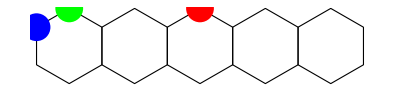

```mathematica
Show[{
	pahgraph[{0,0},1,5,1],
	Graphics[{{PointSize[0.05],Red,Point[{2,1/(√3)}]},{PointSize[0.05],Green,Point[{0,1/(√3)}]},{PointSize[0.05],Blue,Point[{-1/2,1/(2 √3)}]}}]
	}]
```

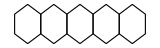

```mathematica
Show[{	pahgraph[{0,0},1,5,1]	}]
```

```mathematica
Show[{	pahgraph[{0,0},1,1,1]	}]
```

-Graphics-

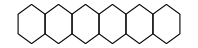

```mathematica
Show[{	pahgraph[{0,0},1,6,1]	}]
```

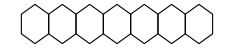

```mathematica
Show[{	pahgraph[{0,0},1,7,1]	}]
```

```mathematica
Show[{	pahgraphMultiRow[{0,0},1,3,3]	}]
```

-Graphics-